# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Nevada","Texas"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2021-12-27

```mathematica
states=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,New Jersey,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Utah,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Arizona→{{2021-12-13,289},{2021-12-14,258},{2021-12-15,160},{2021-12-16,153},{2021-12-17,148},{2021-12-18,124},{2021-12-19,72},{2021-12-20,206},{2021-12-21,246},{2021-12-22,112},{2021-12-23,165},{2021-12-24,17},{2021-12-25,10},{2021-12-26,3},{2021-12-27,138}},California→{{2021-12-13,1425},{2021-12-14,1171},{2021-12-15,1499},{2021-12-16,1459},{2021-12-17,1517},{2021-12-18,1277},{2021-12-19,512},{2021-12-20,1291},{2021-12-21,3487},{2021-12-22,4445},{2021-12-23,3154},{2021-12-24,356},{2021-12-25,51},{2021-12-26,85},{2021-12-27,127}},Colorado→{{2021-12-13,299},{2021-12-14,438},{2021-12-15,515},{2021-12-16,511},{2021-12-17,475},{2021-12-18,469},{2021-12-19,61},{2021-12-20,587},{2021-12-21,491},{2021-12-22,454},{2021-12-23,323},{2021-12-24,121},{2021-12-25,108},{2021-12-26,0},{2021-12-27,0}},Connecticut→{{2021-12-13,161},{2021-12-14,181},{2021-12-15,174},{2021-12-16,182},{2021-12-17,178},{2021-12-18,88},{2021-12-19,93},{2021-12-20,182},{2021-12-21,120},{2021-12-22,202},{2021-12-23,117},{2021-12-24,49},{2021-12-25,0},{2021-12-26,25},{2021-12-27,51}},Florida→{{2021-12-13,187},{2021-12-14,291},{2021-12-15,301},{2021-12-16,146},{2021-12-17,165},{2021-12-18,134},{2021-12-19,149},{2021-12-20,249},{2021-12-21,363},{2021-12-22,159},{2021-12-23,46},{2021-12-24,11},{2021-12-25,12},{2021-12-26,6},{2021-12-27,9}},Georgia→{{2021-12-13,95},{2021-12-14,174},{2021-12-15,257},{2021-12-16,248},{2021-12-17,252},{2021-12-18,118},{2021-12-19,135},{2021-12-20,229},{2021-12-21,188},{2021-12-22,98},{2021-12-23,18},{2021-12-24,1},{2021-12-25,0},{2021-12-26,0},{2021-12-27,1}},Illinois→{{2021-12-13,232},{2021-12-14,345},{2021-12-15,348},{2021-12-16,321},{2021-12-17,317},{2021-12-18,111},{2021-12-19,178},{2021-12-20,261},{2021-12-21,205},{2021-12-22,161},{2021-12-23,12},{2021-12-24,0},{2021-12-25,0},{2021-12-26,0},{2021-12-27,0}},Indiana→{{2021-12-13,104},{2021-12-14,179},{2021-12-15,132},{2021-12-16,102},{2021-12-17,118},{2021-12-18,89},{2021-12-19,49},{2021-12-20,82},{2021-12-21,71},{2021-12-22,69},{2021-12-23,126},{2021-12-24,0},{2021-12-25,0},{2021-12-26,2},{2021-12-27,18}},Kentucky→{{2021-12-13,50},{2021-12-14,45},{2021-12-15,61},{2021-12-16,37},{2021-12-17,42},{2021-12-18,27},{2021-12-19,14},{2021-12-20,10},{2021-12-21,34},{2021-12-22,12},{2021-12-23,47},{2021-12-24,9},{2021-12-25,0},{2021-12-26,51},{2021-12-27,0}},Louisiana→{{2021-12-13,55},{2021-12-14,34},{2021-12-15,65},{2021-12-16,63},{2021-12-17,46},{2021-12-18,41},{2021-12-19,18},{2021-12-20,59},{2021-12-21,39},{2021-12-22,19},{2021-12-23,22},{2021-12-24,2},{2021-12-25,0},{2021-12-26,0},{2021-12-27,9}},Maryland→{{2021-12-13,178},{2021-12-14,312},{2021-12-15,136},{2021-12-16,134},{2021-12-17,162},{2021-12-18,62},{2021-12-19,65},{2021-12-20,95},{2021-12-21,273},{2021-12-22,120},{2021-12-23,26},{2021-12-24,17},{2021-12-25,42},{2021-12-26,0},{2021-12-27,0}},Massachusetts→{{2021-12-13,161},{2021-12-14,531},{2021-12-15,857},{2021-12-16,542},{2021-12-17,601},{2021-12-18,386},{2021-12-19,495},{2021-12-20,717},{2021-12-21,976},{2021-12-22,288},{2021-12-23,36},{2021-12-24,4},{2021-12-25,0},{2021-12-26,0},{2021-12-27,0}},Michigan→{{2021-12-13,146},{2021-12-14,198},{2021-12-15,199},{2021-12-16,173},{2021-12-17,127},{2021-12-18,76},{2021-12-19,107},{2021-12-20,136},{2021-12-21,139},{2021-12-22,113},{2021-12-23,21},{2021-12-24,0},{2021-12-25,0},{2021-12-26,0},{2021-12-27,0}},Minnesota→{{2021-12-13,392},{2021-12-14,285},{2021-12-15,198},{2021-12-16,85},{2021-12-17,167},{2021-12-18,42},{2021-12-19,106},{2021-12-20,54},{2021-12-21,22},{2021-12-22,33},{2021-12-23,47},{2021-12-24,28},{2021-12-25,21},{2021-12-26,15},{2021-12-27,0}},Nebraska→{{2021-12-13,102},{2021-12-14,79},{2021-12-15,64},{2021-12-16,55},{2021-12-17,34},{2021-12-18,27},{2021-12-19,19},{2021-12-20,70},{2021-12-21,33},{2021-12-22,14},{2021-12-23,10},{2021-12-24,20},{2021-12-25,16},{2021-12-26,27},{2021-12-27,92}},New Jersey→{{2021-12-13,159},{2021-12-14,305},{2021-12-15,252},{2021-12-16,260},{2021-12-17,254},{2021-12-18,63},{2021-12-19,125},{2021-12-20,101},{2021-12-21,89},{2021-12-22,102},{2021-12-23,106},{2021-12-24,14},{2021-12-25,0},{2021-12-26,0},{2021-12-27,0}},New York→{{2021-12-13,637},{2021-12-14,925},{2021-12-15,954},{2021-12-16,814},{2021-12-17,647},{2021-12-18,493},{2021-12-19,309},{2021-12-20,473},{2021-12-21,322},{2021-12-22,245},{2021-12-23,119},{2021-12-24,29},{2021-12-25,22},{2021-12-26,8},{2021-12-27,111}},North Carolina→{{2021-12-13,181},{2021-12-14,388},{2021-12-15,131},{2021-12-16,103},{2021-12-17,112},{2021-12-18,73},{2021-12-19,70},{2021-12-20,110},{2021-12-21,201},{2021-12-22,179},{2021-12-23,35},{2021-12-24,43},{2021-12-25,25},{2021-12-26,7},{2021-12-27,0}},North Dakota→{{2021-12-13,127},{2021-12-14,78},{2021-12-15,55},{2021-12-16,18},{2021-12-17,60},{2021-12-18,17},{2021-12-19,28},{2021-12-20,37},{2021-12-21,94},{2021-12-22,58},{2021-12-23,118},{2021-12-24,21},{2021-12-25,9},{2021-12-26,20},{2021-12-27,57}},Ohio→{{2021-12-13,157},{2021-12-14,242},{2021-12-15,221},{2021-12-16,232},{2021-12-17,268},{2021-12-18,115},{2021-12-19,123},{2021-12-20,237},{2021-12-21,174},{2021-12-22,105},{2021-12-23,22},{2021-12-24,1},{2021-12-25,0},{2021-12-26,34},{2021-12-27,0}},Oregon→{{2021-12-13,68},{2021-12-14,57},{2021-12-15,42},{2021-12-16,34},{2021-12-17,48},{2021-12-18,17},{2021-12-19,36},{2021-12-20,35},{2021-12-21,52},{2021-12-22,22},{2021-12-23,18},{2021-12-24,7},{2021-12-25,1},{2021-12-26,10},{2021-12-27,6}},Pennsylvania→{{2021-12-13,93},{2021-12-14,169},{2021-12-15,172},{2021-12-16,157},{2021-12-17,143},{2021-12-18,92},{2021-12-19,38},{2021-12-20,80},{2021-12-21,87},{2021-12-22,107},{2021-12-23,61},{2021-12-24,10},{2021-12-25,0},{2021-12-26,1},{2021-12-27,0}},Tennessee→{{2021-12-13,31},{2021-12-14,67},{2021-12-15,94},{2021-12-16,77},{2021-12-17,47},{2021-12-18,64},{2021-12-19,64},{2021-12-20,64},{2021-12-21,96},{2021-12-22,23},{2021-12-23,8},{2021-12-24,10},{2021-12-25,8},{2021-12-26,3},{2021-12-27,8}},Utah→{{2021-12-13,101},{2021-12-14,160},{2021-12-15,79},{2021-12-16,37},{2021-12-17,146},{2021-12-18,118},{2021-12-19,92},{2021-12-20,153},{2021-12-21,97},{2021-12-22,104},{2021-12-23,71},{2021-12-24,0},{2021-12-25,0},{2021-12-26,22},{2021-12-27,239}},Virginia→{{2021-12-13,119},{2021-12-14,152},{2021-12-15,57},{2021-12-16,34},{2021-12-17,21},{2021-12-18,8},{2021-12-19,8},{2021-12-20,30},{2021-12-21,137},{2021-12-22,98},{2021-12-23,18},{2021-12-24,1},{2021-12-25,0},{2021-12-26,0},{2021-12-27,0}},Washington→{{2021-12-13,296},{2021-12-14,336},{2021-12-15,241},{2021-12-16,254},{2021-12-17,287},{2021-12-18,150},{2021-12-19,90},{2021-12-20,93},{2021-12-21,53},{2021-12-22,45},{2021-12-23,7},{2021-12-24,3},{2021-12-25,1},{2021-12-26,0},{2021-12-27,1}},Wisconsin→{{2021-12-13,243},{2021-12-14,322},{2021-12-15,347},{2021-12-16,313},{2021-12-17,258},{2021-12-18,101},{2021-12-19,81},{2021-12-20,173},{2021-12-21,173},{2021-12-22,174},{2021-12-23,115},{2021-12-24,18},{2021-12-25,0},{2021-12-26,6},{2021-12-27,69}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

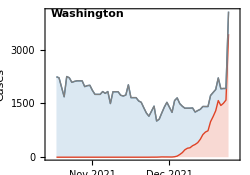

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

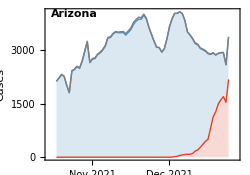
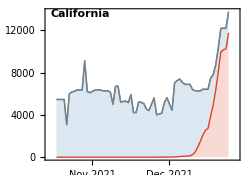
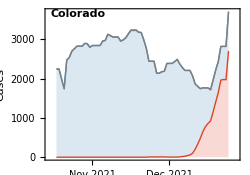
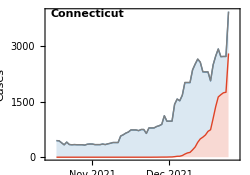
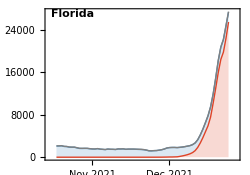
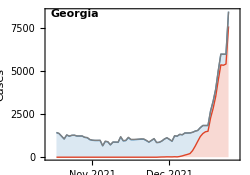
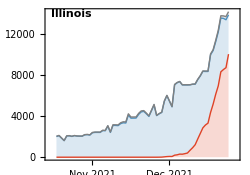
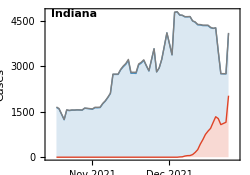
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=20000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png